```mathematica
(*zad7 kontynuacja, czyli dwie tablicy w argumencie*)
```

```mathematica
iloczyn[zbiorA_,zbiorB_]:=Module[{wynik={}},
For[i=1,i≤Length[zbiorA],i++,
If[MemberQ[zbiorB,zbiorA[[i]]],
AppendTo[wynik,zbiorA[[i]]]
];
(*memberQ sprawdza czy element nalezy do listy*)
];
Return[wynik];
]
iloczyn[{2,3,5,7,8},{5,7,,10,13}]
```

{5,7}

```mathematica
MemberQ[{1,3,5,7},5]
```

True

```mathematica
lista={1,4,6,8}
```

{1,4,6,8}

```mathematica
Append[lista,9]
```

{1,4,6,8,9}

```mathematica
lista
```

{1,4,6,8}

```mathematica
lista=Append[lista,9]
```

{1,4,6,8,9}

```mathematica
lista
```

{1,4,6,8,9}

```mathematica
AppendTo[lista,11]
```

{1,4,6,8,9,11}

```mathematica
lista
```

{1,4,6,8,9,11}

```mathematica
suma[zbiorA_,zbiorB_]:=Module[{wynik=zbiorB},
For[i=1,i≤Length[zbiorA],i++,
If[!MemberQ[zbiorB,zbiorA[[i]]],
AppendTo[wynik,zbiorA[[i]]]
];
];
Return[wynik];
]
```

```mathematica
suma[{2,3,5,7,8},{5,7,10,13}]
```

{5,7,10,13,2,3,8}

```mathematica
roznica[zbiorA_,zbiorB_]:=Module[{wynik={}},
For[i=1,i≤Length[zbiorA],i++,
If[!MemberQ[zbiorB,zbiorA[[i]]],
AppendTo[wynik,zbiorA[[i]]]
];
];
Return[wynik];
]
```

```mathematica
roznica[{2,3,5,7,8},{5,7,10,13}]
```

{2,3,8}

```mathematica
Delete[{3,4,6,8},2] (*usunie drugi element*)
```

{3,6,8}

```mathematica
{1,2,0}+{3,4,7}
```

{4,6,7}

```mathematica
(*zad8*)
(*czy nalezy dokola? sprawdzamy odleglosc od srodka*)
```

```mathematica
losujPunkty[n_]:=Module[{x,y,punkt={},wKole={},pozaKolem={},r1,r2},
For[i=1,i≤n,i++,
x=RandomReal[{-1,1}];
y=RandomReal[{-1,1}];
punkt={x,y};
If[Sqrt[x^2+y^2]≤1,
AppendTo[wKole,punkt],
AppendTo[pozaKolem,punkt];
];
];
r1=ListPlot[wKole,PlotStyle->{Red}];
r2=ListPlot[pozaKolem,PlotStyle->{Blue}];
Print[N[4*Length[wKole]/n]];
Show[{r1,r2},Frame->True, AspectRatio->Automatic, PlotRange->All]
]
```

3.1436

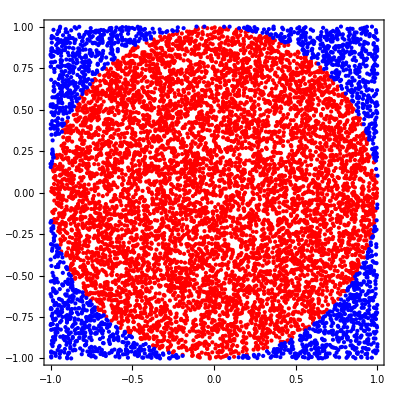

```mathematica
losujPunkty[10000]
```